```mathematica
data = Import["D:\\Dev\\python\\predictor\\datas\\EURUSD_H1.csv","Table"];
```

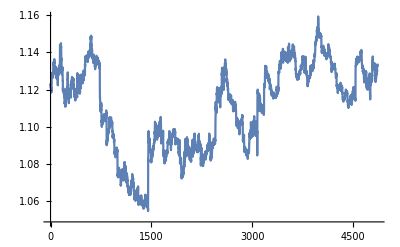

```mathematica
shift = 64*12;
start = -2^15+shift;
end =start+2^12+shift;
opens = data[[start;;end,3]];
fullopens = data[[start;;end+1024,3]];
ListLinePlot[opens,Joined->True]
```

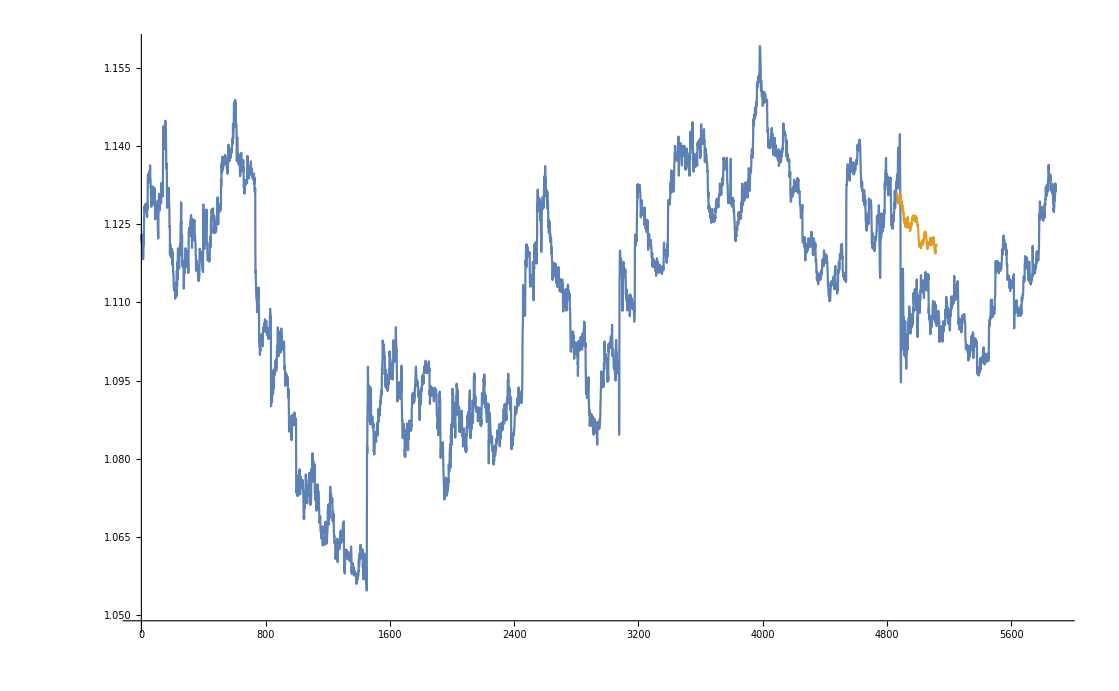

```mathematica
tsmod=TimeSeriesModelFit[opens,"MA"];
forecast = TimeSeriesForecast[tsmod,  {256}];
ListLinePlot[{fullopens,forecast}]
```